## First the formulae

```mathematica
CalculateInOutFormulaAll[g_]:=CalculateInOutFormulaAll[g,VertexList[g]]
```

```mathematica
MyLetter[node_]:=FromCharacterCode[ToCharacterCode["a"]+node-1]
```

```mathematica
RepNode[node_]:=Symbol[MyLetter[node]<>ToString[node]]->MyLetter[node]
```

```mathematica
VertexRepl[repl_]:=Table[Symbol[MyLetter[k]<>ToString[k]]->Symbol[MyLetter[repl[k]]],{k,Keys[repl]}]
```

```mathematica
VertexRepl[Association[{2->1,4->3,5->3}]]
```

{b2→a,d4→c,e5→c}

```mathematica
IdempAssoc[sets_]:=Block[{result=Association[]},
Table[result[k]=k,{k,sets}];
result
]
```

```mathematica
IdempAssoc[{1,2,3,5,4}]
```

<|1→1,2→2,3→3,5→5,4→4|>

```mathematica
RepLetters[n_:10]:=Table[Symbol[MyLetter[k]]->x,{k,n}]
```

```mathematica
CalculateInOutFormulaAll[g_,sets_]:=CalculateInOutFormulaAll[g,sets,IdempAssoc[sets]]
```

```mathematica
CalculateInOutFormulaAll[g_,sets_, repl2_]:=Block[{
currentEdge, 
edges, 
pos,
isInOut, gContract, gRemove, gIn, gOut, result, resIn, resOut, resContract, resRemove, repVertex, in, out,inVertex,outVertex,
node,
  maxRep, minRep, newRep=repl2},
If[VertexCount[g]==0,
Print["VertexCount is zero",g,sets];
Return[1]
];
(* if there is no set, we have a problem *)
If[Length[sets]==0,
Print["No more sets"];
Interrupt[];
];
(* if there is only one set, we are done *)
If[Length[sets]==1,
node=First[sets];
result=FindFullFormulaWithPrefix[g,MyLetter[node]]/.VertexRepl[newRep];
Return[result];
];

(* there is more than 1 set : we define in to be the first set, out to be thejoin of the rest *)
in=First[sets];
out=Rest[sets];

(* the whole goal is to remove the  in *)
(* as long as there is an edge between in and out we remove and contract it and recurse *)
edges=EdgeList[g,in<->_];
If[edges≠{},
currentEdge=First[edges];
If[currentEdge[[1]]≠in, 
(* make sure the first vertex is in "in" an dthe second in "out" *)
currentEdge=UndirectedEdge[currentEdge[[2]],currentEdge[[1]]]
];
(* the remove is easy, it uses the same vertex set and the same replacement *)
gRemove=EdgeDelete[g,currentEdge];
resRemove=CalculateInOutFormulaAll[gRemove,sets,repl2];

(* no wthe contract *)
inVertex = currentEdge[[1]];
outVertex = currentEdge[[2]];
minRep=Min[newRep[inVertex],newRep[outVertex]];
newRep[inVertex]=minRep;
newRep[outVertex]=minRep;
gContract=GContract[g,currentEdge];
repVertex={inVertex->outVertex}; (* replace the in by the out since we want ot get rid of the in *)
gContract=Graph[VertexList[gContract]/.repVertex,Map[#[[1]]<->#[[2]]/.repVertex&,EdgeList[gContract]]];
resContract=CalculateInOutFormulaAll[gContract,sets,newRep];
result=resRemove-resContract;
Return[result]
];

(* there are no more edges between in and out so we compute in and recurse with the rest *)
gIn=Subgraph[g,in];
gOut=Subgraph[g,out];
resIn=If[VertexCount[gIn]==0,1,FindFullFormulaWithPrefix[gIn, MyLetter[First[VertexList[gIn]]]]/.VertexRepl[newRep]];
resOut=If[VertexCount[gOut]==0,1,CalculateInOutFormulaAll[gOut,Rest[sets],repl2]];
Return[resIn*resOut]
]
```

## First small steps

```mathematica
CalculateInOutFormulaAll[CycleGraph[4],Reverse[Range[4]]]//Factor
```

a (-1+b) (3-2 c-d+c d)

```mathematica
Simplify[a (-1+b) (3-2 c-d+c d)]
```

a (-1+b) (3+c (-2+d)-d)

```mathematica
CalculateInOutFormulaAll[CycleGraph[4],Range[4]]
```

-3 a+a b+a c-b (-a+a c)+a d-a (-c+c d)+a (b-b d+b (-c+c d))

```mathematica
Simplify[-3 a+a b+a c-b (-a+a c)+a d-a (-c+c d)+a (b-b d+b (-c+c d))]
```

a (-1+b) (3+c (-2+d)-d)

```mathematica
Simplify[CalculateInOutFormulaAll[CycleGraph[4],Range[4]]-CalculateInOutFormulaAll[CycleGraph[4],Reverse[Range[4]]]]
```

0

## Now we do some tests

```mathematica
CalculateInOutFormulaAll[CompleteGraph[3],{3,2,1}]//Factor//TraditionalForm
```

a (b-1) (c-2)

```mathematica
CalculateInOutFormulaAll[CompleteGraph[3],{1,2,3}]//Factor//TraditionalForm
```

a (b-1) (c-2)

```mathematica
CalculateInOutFormulaAll[WheelGraph[6]]
```

-30 a+8 a b+2 a c-(-a+a b) c+4 a d-2 (-a+a b) d+c (a-a b+(-a+a b) d)+8 a e-b (-a+a e)-2 c (-a+a e)-4 d (-a+a e)-3 a (-b+b e)+b (a-a d+d (-a+a e))+2 c (a-a d+d (-a+a e))+c (2 a-a b-a e+a (-b+b e))+a (b-b d+d (-b+b e))-b (-a+a c-c (-a+a e)+c (a-a d+d (-a+a e)))+8 a f-b (-a+a f)-c (-a+a f)-2 d (-a+a f)-4 a (-e+e f)+b (a-a f+d (-a+a f))+c (a-a f+d (-a+a f))+b (2 a-a e-a f+a (-e+e f))+c (2 a-a e-a f+a (-e+e f))+2 a (d-d f+d (-e+e f))-b (-a+a f-c (-a+a f)+c (a-a f+d (-a+a f)))-b (-2 a+a e+a f-a (-e+e f)+c (2 a-a e-a f+a (-e+e f)))-b (-4 a+a d+a e-d (-a+a e)+2 a f-d (-a+a f)-a (-e+e f)+a (d-d f+d (-e+e f)))-a (-c+c f-c (-e+e f)+c (d-d f+d (-e+e f)))+a (4 b-b c-b d-b e+c (-b+b e)+d (-b+b e)-c (b-b d+d (-b+b e))-b f+b (-e+e f)-b (d-d f+d (-e+e f))+b (-c+c f-c (-e+e f)+c (d-d f+d (-e+e f))))

```mathematica
Factor[Out[804]]
```

a (-1+b) (-2+c) (-15+7 d+6 e-3 d e+4 f-2 d f-2 e f+d e f)

```mathematica
a (-1+b) (-2+c) (-15+7 d+6 e-3 d e+4 f-2 d f-2 e f+d e f)/.RepLetters[10]
```

(-2+x) (-1+x) x (-15+17 x-7 x^2+x^3)

```mathematica
Animate[Plot3D[-15+7 d+6 e-3 d e+4 f-2 d f-2 e f+d e f,{d,-10,10},{e,-10,10},PlotRange->{Full,Full,{0,1000}}],{f,-10,10}]
```

```mathematica
RepLetters[10]
```

{a→x,b→x,c→x,d→x,e→x,f→x,g→x,h→x,i→x,j→x}

```mathematica
CalculateInOutFormulaAll[WheelGraph[6],Reverse[Range[6]]]//TraditionalForm
```

f (e (d (c (a b-a)-2 a b+2 a)-2 c (a b-a)+4 a b-4 a)-2 d (c (a b-a)-2 a b+2 a)+4 c (a b-a)-8 a b+8 a)-3 e (d (c (a b-a)-2 a b+2 a)-2 c (a b-a)+4 a b-4 a)+7 d (c (a b-a)-2 a b+2 a)-15 c (a b-a)+30 a b-30 a

```mathematica
Simplify[(a (b (c (d (e f-e)+d (-f)+d)-c (e f-e)+c f-c)-c (d (b e-b)+b (-d)+b)+c (b e-b)+b (-c)-b (d (e f-e)+d (-f)+d)+d (b e-b)-b d+b (e f-e)-b e-b f+4 b)-b (c (d (a e-a)+a (-d)+a)-c (a e-a)+a c-a)-b (c (d (a f-a)+a (-f)+a)-c (a f-a)+a f-a)+c (d (a b-a)+a (-b)+a)-b (c (a (e f-e)+a (-e)-a f+2 a)-a (e f-e)+a e+a f-2 a)+c (a (b e-b)+a (-b)-a e+2 a)-c (a b-a)-b (a (d (e f-e)+d (-f)+d)-d (a e-a)-d (a f-a)+a d-a (e f-e)+a e+2 a f-4 a)+a (d (b e-b)+b (-d)+b)+b (d (a e-a)+a (-d)+a)+b (d (a f-a)+a (-f)+a)-2 d (a b-a)+b (a (e f-e)+a (-e)-a f+2 a)-3 a (b e-b)-b (a e-a)-b (a f-a)+8 a b-a (c (d (e f-e)+d (-f)+d)-c (e f-e)+c f-c)+2 c (d (a e-a)+a (-d)+a)+c (d (a f-a)+a (-f)+a)+c (a (e f-e)+a (-e)-a f+2 a)-2 c (a e-a)-c (a f-a)+2 a c+2 a (d (e f-e)+d (-f)+d)-4 d (a e-a)-2 d (a f-a)+4 a d-4 a (e f-e)+8 a e+8 a f-30 a)-(f (e (d (c (a b-a)-2 a b+2 a)-2 c (a b-a)+4 a b-4 a)-2 d (c (a b-a)-2 a b+2 a)+4 c (a b-a)-8 a b+8 a)-3 e (d (c (a b-a)-2 a b+2 a)-2 c (a b-a)+4 a b-4 a)+7 d (c (a b-a)-2 a b+2 a)-15 c (a b-a)+30 a b-30 a)]
```

0

```mathematica
CalculateInOutFormulaAll[WheelGraph[5],Reverse[Range[5]]]//Factor//TraditionalForm
```

{<|5→1,4→3,3→2|>,3,1}

$Aborted

```mathematica
CalculateInOutFormulaAll[WheelGraph[5],Range[5]]//Factor//TraditionalForm
```

(c-1) d (a a1 b-a a1-4 a b+5 a-2 a1 b+3 a1+9 b-14)

```mathematica
CalculateInOutFormulaAll[CycleGraph[6]]//Factor//TraditionalForm
```

```mathematica
CycleGraph[6, VertexLabels->"Name"]//EdgeList
```

{1<->2,1<->6,2<->3,3<->4,4<->5,5<->6}

```mathematica
CalculateInOutFormulaAll[EdgeDelete[CycleGraph[6],1<->6]]//Factor//TraditionalForm
```

(a-1) (b-1) (c-1) (d-1) (e-1) f

## Now for some grofs

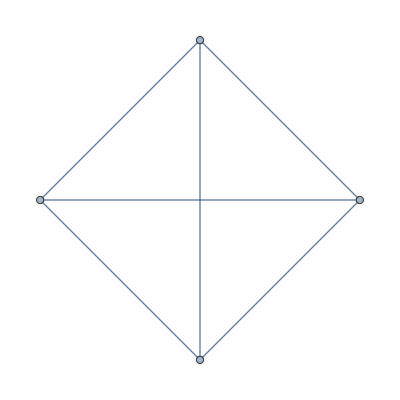
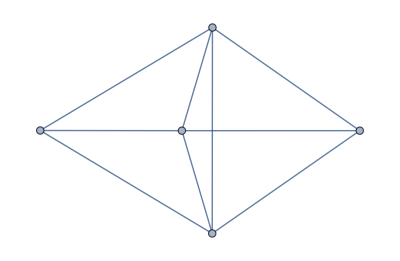
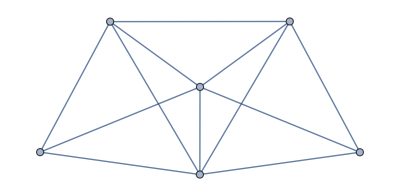
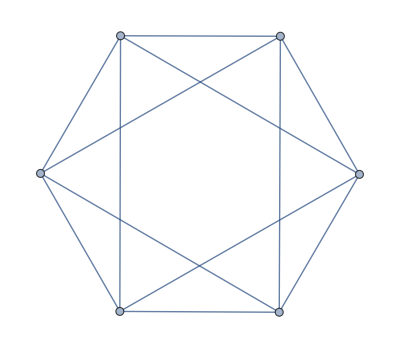

```mathematica
Monitor[Table[ReadGrof[k],{k,4}],k]
```

```mathematica
CalculateInOutFormulaAll[Graph[{1,2},{}]]
```

a b

```mathematica
Monitor[Table[CalculateInOutFormulaAll[ReadGrof[k]],{k,4}],k]
```

{-6 a+2 a b+2 a c-b (-a+a c)+2 a d-b (-a+a d)-a (-c+c d)+a (2 b-b c-b d+b (-c+c d)),18 a-5 a b-3 a c+(-a+a b) c-6 a d+b (-a+a d)+2 c (-a+a d)+a (-b+b d)-b (2 a-a c-a d+c (-a+a d))-4 a e+c (-a+a e)+a (-b+b e)+2 a (-d+d e)-b (2 a-a d-a e+a (-d+d e))-a (2 c-c d-c e+c (-d+d e))+a (-6 b+2 b c+2 b d-c (-b+b d)+2 b e-c (-b+b e)-b (-d+d e)+b (2 c-c d-c e+c (-d+d e))),-54 a+10 a b+8 a c-a (-b+b c)+22 a d-b (-a+a d)-c (-a+a d)-4 a (-b+b d)-2 a (-c+c d)+c (2 a-a b-a d+a (-b+b d))+2 a e-(-a+a b) e-(-a+a c) e-4 (-a+a d) e+c (2 a-2 a d+(-a+a d) e)+a (2 b-2 b d+(-b+b d) e)+12 a f-b (-a+a f)-2 e (-a+a f)-a (-b+b f)-2 a (-c+c f)-6 a (-d+d f)+b (2 a-a d-a f+a (-d+d f))+2 c (2 a-a d-a f+a (-d+d f))+a (2 b-b d-b f+b (-d+d f))+2 a (2 d-d e-d f+e (-d+d f))-b (-6 a+2 a c+2 a d-a (-c+c d)+2 a f-a (-c+c f)-a (-d+d f)+c (2 a-a d-a f+a (-d+d f)))-b (-6 a+3 a d+a e-(-a+a d) e+2 a f-e (-a+a f)-a (-d+d f)+a (2 d-d e-d f+e (-d+d f)))-a (-6 c+3 c d+c e-(-c+c d) e+2 c f-e (-c+c f)-c (-d+d f)+c (2 d-d e-d f+e (-d+d f)))+a (18 b-5 b c-8 b d+c (-b+b d)+b (-c+c d)-b e+(-b+b c) e+2 (-b+b d) e-c (2 b-2 b d+(-b+b d) e)-4 b f+e (-b+b f)+b (-c+c f)+2 b (-d+d f)-c (2 b-b d-b f+b (-d+d f))-b (2 d-d e-d f+e (-d+d f))+b (-6 c+3 c d+c e-(-c+c d) e+2 c f-e (-c+c f)-c (-d+d f)+c (2 d-d e-d f+e (-d+d f)))),-64 a+19 a b+9 a c-(-a+a b) c-a (-b+b c)+18 a d-b (-a+a d)-2 c (-a+a d)-3 a (-b+b d)+c (2 a-a b-a d+a (-b+b d))+4 a e-4 (-a+a b) e-2 (-a+a c) e-4 (-a+a d) e+c (2 a-2 a b+(-a+a b) e)+b (2 a-2 a d+(-a+a d) e)+2 c (2 a-2 a d+(-a+a d) e)+a (2 b-2 b d+(-b+b d) e)-b (-4 a+3 a c+a d-c (-a+a d)-(-a+a c) e+c (2 a-2 a d+(-a+a d) e))+14 a f-c (-a+a f)-4 e (-a+a f)-4 a (-b+b f)-a (-c+c f)-4 a (-d+d f)+c (2 a-a e-a f+e (-a+a f))+c (2 a-a b-a f+a (-b+b f))+a (2 b-b e-b f+e (-b+b f))+b (2 a-a d-a f+a (-d+d f))+c (2 a-a d-a f+a (-d+d f))+2 a (2 d-d e-d f+e (-d+d f))-b (-4 a+a c+a d+2 a f-a (-c+c f)-a (-d+d f)+c (2 a-a d-a f+a (-d+d f)))-b (-6 a+3 a d+a e-(-a+a d) e+2 a f-e (-a+a f)-a (-d+d f)+a (2 d-d e-d f+e (-d+d f)))-a (-4 c+c d+c e+2 c f-e (-c+c f)-c (-d+d f)+c (2 d-d e-d f+e (-d+d f)))+a (14 b-4 b c-4 b d+c (-b+b d)-2 b e+(-b+b c) e+(-b+b d) e-c (2 b-2 b d+(-b+b d) e)-4 b f+c (-b+b f)+2 e (-b+b f)+b (-d+d f)-c (2 b-b e-b f+e (-b+b f))-b (2 d-d e-d f+e (-d+d f))+b (-4 c+c d+c e+2 c f-e (-c+c f)-c (-d+d f)+c (2 d-d e-d f+e (-d+d f))))}

```mathematica
TableForm[Map[Factor,Out[534]]]
```

a (-1+b) (-2+c) (-3+d)
a (-1+b) (-2+c) (9-4 d-2 e+d e)
a (-1+b) (-2+c) (-27+16 d+5 e-4 d e+6 f-4 d f-e f+d e f)
a (-1+b) (-2+c) (-32+13 d+9 e-4 d e+7 f-3 d f-2 e f+d e f)

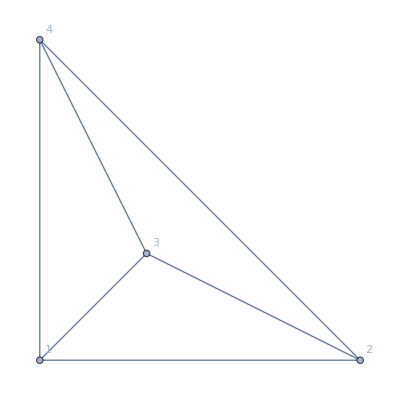
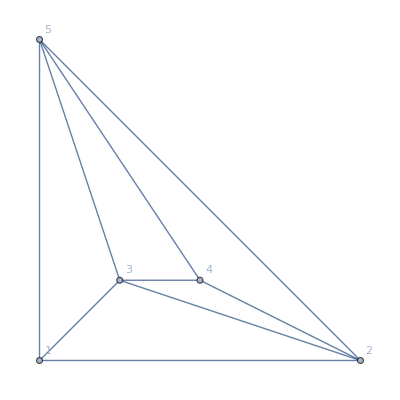
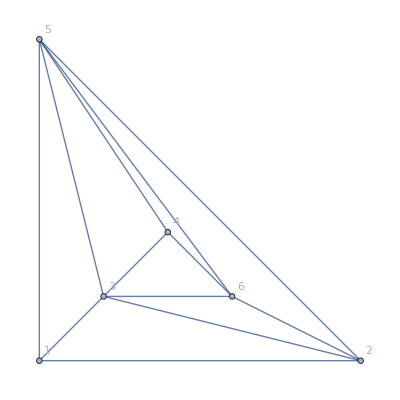
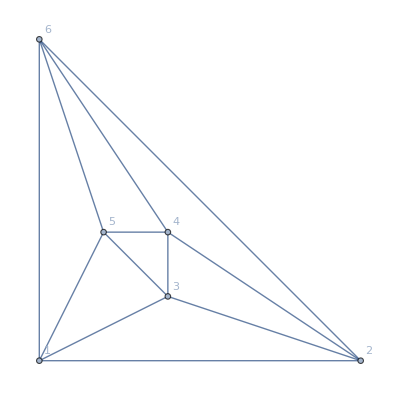
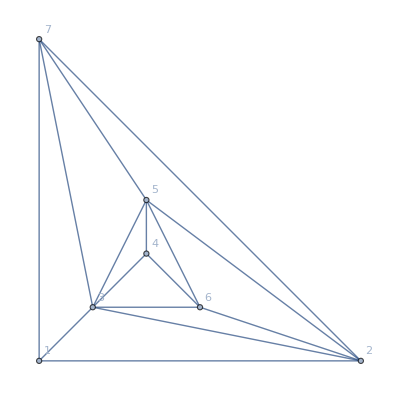
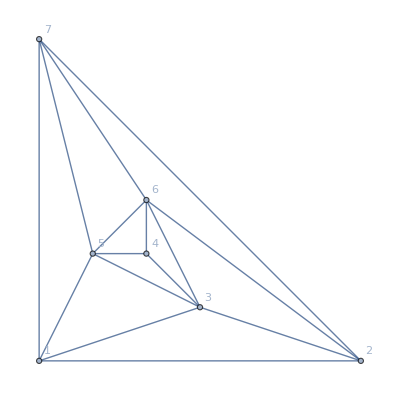
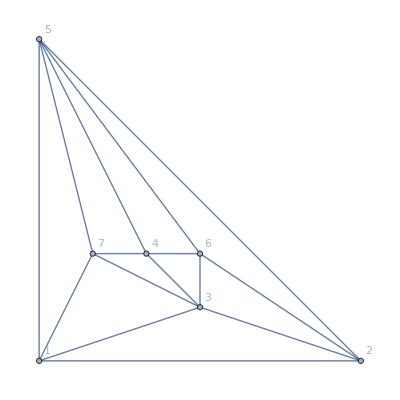
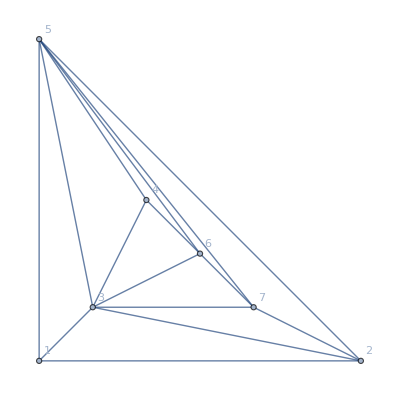

```mathematica
Monitor[Table[Graph[ReadGrof[k],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"],{k,15}],k]
```

```mathematica
Monitor[TableForm[
Table[With[{g=ReadGrof[k]},Framed[Column[{Pane[Labeled[Style[Factor[CalculateInOutFormulaAll[g]],LineIndent->0,TextAlignment->Left],Style[ChromaticPolynomial[g,4]/24,Red,Bold]],500],Graph[g,GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]}]]],{k,15}]
],k]
```

a (-1+b) (-2+c) (-3+d)1
-Graphics-
a (-1+b) (-2+c) (9-4 d-2 e+d e)1
-Graphics-
a (-1+b) (-2+c) (-27+16 d+5 e-4 d e+6 f-4 d f-e f+d e f)1
-Graphics-
a (-1+b) (-2+c) (-32+13 d+9 e-4 d e+7 f-3 d f-2 e f+d e f)4
-Graphics-
a (-1+b) (-2+c) (81-52 d-20 e+16 d e-18 f+13 d f+4 e f-4 d e f-18 g+12 d g+5 e g-4 d e g+4 f g-3 d f g-e f g+d e f g)1
-Graphics-
a (-1+b) (-2+c) (96-58 d-22 e+17 d e-18 f+13 d f+4 e f-4 d e f-21 g+13 d g+5 e g-4 d e g+4 f g-3 d f g-e f g+d e f g)4
-Graphics-
a (-1+b) (-2+c) (105-55 d-24 e+16 d e-23 f+13 d f+5 e f-4 d e f-23 g+13 d g+5 e g-4 d e g+5 f g-3 d f g-e f g+d e f g)5
-Graphics-
a (-1+b) (-2+c) (81-52 d-14 e+13 d e-24 f+16 d f+4 e f-4 d e f-18 g+12 d g+3 e g-3 d e g+6 f g-4 d f g-e f g+d e f g)1
-Graphics-
a (-1+b) (-2+c) (-27+16 d+5 e-4 d e+6 f-4 d f-e f+d e f) (-3+g)1
-Graphics-
a (-1+b) (-2+c) (-243+208 d+44 e-64 d e+45 f-52 d f-4 e f+16 d e f+54 g-48 d g-11 e g+16 d e g-10 f g+12 d f g+e f g-4 d e f g+54 h-52 d h-8 e h+16 d e h-9 f h+13 d f h-4 d e f h-12 g h+12 d g h+2 e g h-4 d e g h+2 f g h-3 d f g h+d e f g h)1
-Graphics-
a (-1+b) (-2+c) (-315+190 d+92 e-68 d e+69 f-45 d f-19 e f+17 d e f+60 g-39 d g-20 e g+16 d e g-13 f g+9 d f g+4 e f g-4 d e f g+69 h-43 d h-20 e h+16 d e h-15 f h+10 d f h+4 e f h-4 d e f h-14 g h+9 d g h+5 e g h-4 d e g h+3 f g h-2 d f g h-e f g h+d e f g h)5
-Graphics-
a (-1+b) (-2+c) (-243+172 d+80 e-64 d e+45 f-40 d f-16 e f+16 d e f+54 g-39 d g-20 e g+16 d e g-10 f g+9 d f g+4 e f g-4 d e f g+54 h-40 d h-20 e h+16 d e h-9 f h+9 d f h+4 e f h-4 d e f h-12 g h+9 d g h+5 e g h-4 d e g h+2 f g h-2 d f g h-e f g h+d e f g h)1
-Graphics-
a (-1+b) (-2+c) (-243+169 d+56 e-52 d e+72 f-52 d f-16 e f+16 d e f+54 g-39 d g-14 e g+13 d e g-16 f g+12 d f g+4 e f g-4 d e f g+54 h-39 d h-12 e h+12 d e h-18 f h+13 d f h+4 e f h-4 d e f h-12 g h+9 d g h+3 e g h-3 d e g h+4 f g h-3 d f g h-e f g h+d e f g h)1
-Graphics-
a (-1+b) (-2+c) (-288+169 d+76 e-52 d e+81 f-52 d f-20 e f+16 d e f+64 g-39 d g-19 e g+13 d e g-18 f g+12 d f g+5 e f g-4 d e f g+63 h-39 d h-16 e h+12 d e h-18 f h+13 d f h+4 e f h-4 d e f h-14 g h+9 d g h+4 e g h-3 d e g h+4 f g h-3 d f g h-e f g h+d e f g h)4
-Graphics-
a (-1+b) (-2+c) (-288+193 d+87 e-69 d e+56 f-45 d f-17 e f+17 d e f+54 g-39 d g-20 e g+16 d e g-10 f g+9 d f g+4 e f g-4 d e f g+63 h-43 d h-20 e h+16 d e h-12 f h+10 d f h+4 e f h-4 d e f h-12 g h+9 d g h+5 e g h-4 d e g h+2 f g h-2 d f g h-e f g h+d e f g h)4
-Graphics-